```mathematica
Clear["Global`*"]
```

```mathematica
(*Funktionen*)
GiveX[l_,y_]:=Extract[l,Position[l,{xs_,ys_}/;ys==y]][[1,1]]
GiveX[l_,Range_List]:=Extract[l,Position[l,{xs_,ys_}/;ys>=Range[[1]]&&ys<=Range[[2]]]][[1,1]]
GiveY[l_,x_]:=Extract[l,Position[l,{xs_,ys_}/;xs==x]][[1,2]]
GiveY[l_,Range_List]:=Extract[l,Position[l,{xs_,ys_}/;xs>=Range[[1]]&&xs<=Range[[2]]]][[1,2]]
GiveXY[l_,z_]:=Extract[l,Position[l,{xs_,ys_,zs_}/;zs==z]][[1]][[{1,2}]]
FindMaximumList[l_]:={GiveX[l,Max[l]],Max[l]}
```

```mathematica
(*Parameter*)
M=50.; (*Masse des Gegengewichts*)
m=1.; (*Masse des Geschosses*)
L=3.5; (*gewählte Länge des Wurfarms*)
d=0.1; (*Dicke des Wurfarms*)
Tm=0.;(*Plot und Integrations Range*)
Tp=2.;
θ0=-1.2; (*Startwinkel des Wurfarms, wenn keine Einschränkung aus Geometrie*)
n=2000;(*Anzahl der Auswertungspunkte*)
(*Konstanten*)
g=9.81;
ρ=670.;(*Dichte Holz*)
```

```mathematica
(*Startwerte*)
h0=0.7 (*Länge der Aufhängung des Gegengewichts*)
x0=0.02(*Abstand Aufhängung des Wurfarms zum SP, guter Start: L/4*)
```

0.7

0.02

```mathematica
(*abgeleitete Parameter*)
L1[L_,x_]:=L/2-x
L2[L_,x_]:=L/2+x
μ[L_]:=L d^2 ρ
V[L_,x_]:=M g L1[L,x] - m g L2[L,x] - μ[L] g x
i[L_,x_]:=μ[L](1/12 L^2+x^2)+m L2[L,x]^2+M L1[L,x]^2
μ[L]
```

23.45

```mathematica
(*Einschränkung an den Startwinkel aus Geometrie*)
(*Achtung: θstart muss größer als Pi/4=0.785 sein, sonst wird der optimale Abwurfwinkel nie erreicht*)
(*θstart[L_,h_,x_]:=Re[-ArcCos[(L1[L,x] Sin[Pi/4]+h)/L2[L,x]]HeavisideTheta[L2[L,x]-L1[L,x] Sin[Pi/4]-h]+θ0 HeavisideTheta[L1[L,x] Sin[Pi/4]+h-L2[L,x]]]*)
θstart[L_,h_,x_]:=θ0
θstart[L,h0,x0]
```

-1.2

```mathematica
(*Lösung der DGL*)
s[L_,h_,x_]:=NDSolve[{i[L,x] θ''[t]==M L1[L,x] h φ''[t]Sin[φ[t]+θ[t]]+M L1[L,x] h φ'[t]^2 Cos[φ[t]+θ[t]]+V[L,x] Cos[θ[t]],h φ''[t]==L1[L,x] θ''[t]Sin[φ[t]+θ[t]]+L1[L,x] θ'[t]^2 Cos[φ[t]+θ[t]]-g Sin[φ[t]],θ[0]==θstart[L,h,x],θ'[0]==0,φ[0]==0,φ'[0]==0},{θ,φ},{t,Tm,Tp}]
```

```mathematica
Pv[L_,h_,x_,t0_]:=Block[{S},S=s[L,h,x];Plot[Evaluate[L2[L,x] θ'[t]/.S],{t,Tm,Tp},PlotRange->All,GridLines->{{{t0,Red}},None},PlotLabel->"Geschossgeschwindigkeit",AxesLabel->{"t","v(t)"}]]
Pth[L_,h_,x_,t0_]:=Block[{S},S=s[L,h,x];Plot[Evaluate[θ[t]/.S],{t,Tm,Tp},PlotRange->All,GridLines->{{{t0,Red}},None},PlotLabel->"Winkel",AxesLabel->{"t","θ(t)"}]]
```

```mathematica
thList[L_,h_,x_]:=Block[{S},S=s[L,h,x];Table[{t,(θ[t]/.S)[[1]]},{t,Tm,Tp,(Tp-Tm)/n}]]
omList[L_,h_,x_]:=Block[{S},S=s[L,h,x];Table[{t,(θ'[t]/.S)[[1]]},{t,Tm,Tp,(Tp-Tm)/n}]]
vList[L_,h_,x_]:=Block[{S},S=s[L,h,x];Table[{t,(L2[L,x] θ'[t]/.S)[[1]]},{t,Tm,Tp,(Tp-Tm)/n}]]
tWurf[L_,h_,x_]:=GiveX[thList[L,h,x],{Pi/4,Pi/2}]
```

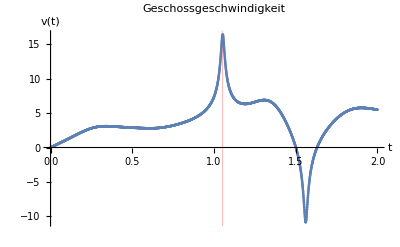

```mathematica
t0=tWurf[L,h0,x0];
Show[Pv[L,h0,x0,t0],ListPlot[vList[L,h0,x0]]]
```

```mathematica
(*maximale Geschossgeschwindigkeit*)
max=FindMaximumList[vList[L,h0,x0]];
tmax=max[[1]]
vmax=max[[2]]
vMax[L_,h_,x_]:=FindMaximumList[vList[L,h,x]][[2]]
(*sollte 45° möglichst nahe kommen*)
θopt=GiveY[thList[L,h0,x0],tmax];
θopt/(2Pi) *360
(*Wurfweite, Abwurfhöhe aus Geometrie*)
smax=vmax Cos[Pi/2-θopt]/g(vmax Sin[Pi/2-θopt]+Sqrt[(vmax Sin[Pi/2-θopt])^2+2 g (L Sin[θopt]+h0)])
```

1.053

16.4099

45.488

30.3827

```mathematica
(*Geschossgeschwindigkeit bei 45°*)
tWurf[L_,h_,x_]:=GiveX[thList[L,h,x],{Pi/4,Pi/2}]
thWurf[L_,h_,x_]:=GiveY[thList[L,h,x],{tWurf[L,h,x],Tp}]
vWurf[L_,h_,x_]:=GiveY[vList[L,h,x],{tWurf[L,h,x],Tp}]
sMax[L_,h_,x_]:=vWurf[L,h,x] Cos[Pi/4]/g(vWurf[L,h,x] Sin[Pi/4]+Sqrt[(vWurf[L,h,x] Sin[Pi/4])^2+2 g (L Sin[Pi/4]+h)])
thWurf[L,h0,x0]/(2Pi)*360
sMax[L,h0,x0]
```

45.488

30.3241

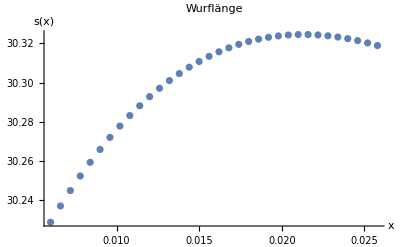

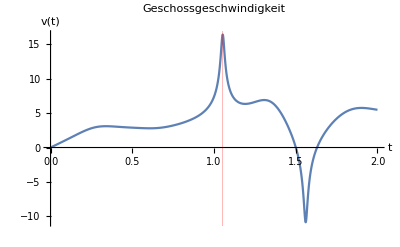

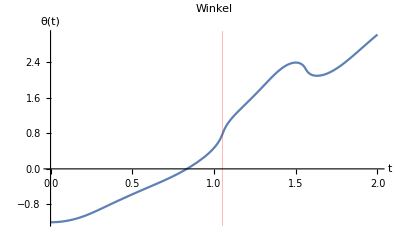

Abwurfzeitpunkt t0 = 1.053

neuer Startwert für h0 = 0.7

neuer Startwert für x0 = 0.021

smax = 30.3246

```mathematica
(*1D Analyse in x*)
sMaxx=Table[{x,sMax[L,h0,x]},{x,0.3x0,1.3 x0,0.6x0/20}];
ListPlot[sMaxx,PlotLabel->"Wurflänge",AxesLabel->{"x","s(x)"}]
xmax=GiveX[sMaxx,Max[sMaxx]];
t0=tWurf[L,h0,xmax];
Pv[L,h0,xmax,t0]
Pth[L,h0,xmax,t0]
Print["Abwurfzeitpunkt t0 = ",t0]
Print["neuer Startwert für h0 = ",h0]
Print["neuer Startwert für x0 = ",xmax]
Print["smax = ",sMax[L,h0,xmax]]
x0=xmax;
```

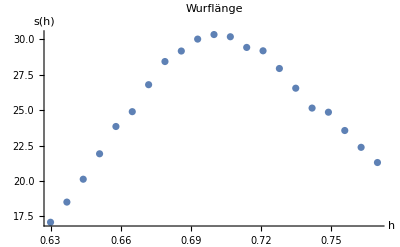

-Graphics-

-Graphics-

Abwurfzeitpunkt t0 = 1.053

neuer Startwert für h0 = 0.7

neuer Startwert für x0 = 0.021

smax = 30.3246

```mathematica
(*1D Analyse in h*)
sMaxh=Table[{h,sMax[L,h,x0]},{h,0.9h0,1.1 h0,0.2h0/20}];
ListPlot[sMaxh,PlotLabel->"Wurflänge",AxesLabel->{"h","s(h)"}]
hmax=GiveX[sMaxh,Max[sMaxh]];
t0=tWurf[L,hmax,x0];
Pv[L,hmax,x0,t0]
Pth[L,hmax,x0,t0]
Print["Abwurfzeitpunkt t0 = ",t0]
Print["neuer Startwert für h0 = ",hmax]
Print["neuer Startwert für x0 = ",x0]
Print["smax = ",sMax[L,hmax,x0]]
h0=hmax;
```

```mathematica
(*1D Analyse in x*)
(*vMaxx=Table[{x,vMax[L,h0,x]},{x,0.5x0,2.5 x0,x0/30}];
ListPlot[vMaxx]
xmax=GiveX[vMaxx,Max[vMaxx]];
Pv[L,h0,xmax]
Print["neuer Startwert für h0 = ",h0]
Print["neuer Startwert für x0 = ",xmax]
Print["vmax = ",vMax[L,h0,xmax]]
x0=xmax;*)
```

```mathematica
(*1D Analyse in h*)
(*vMaxh=Table[{h,vMax[L,h,x0]},{h,0.5h0,1.5 h0,h0/30}];
ListPlot[vMaxh]
hmax=GiveX[vMaxh,Max[vMaxh]];
Pv[L,hmax,x0]
Print["neuer Startwert für h0 = ",hmax]
Print["neuer Startwert für x0 = ",x0]
Print["vmax = ",vMax[L,hmax,x0]]
h0=hmax;*)
```

```mathematica
(*2D Analyse in h und x*)
(*vMaxhx=Flatten[Table[{h,x,vMax[L,h,x]},{h,0.5h0,1.5 h0,h0/10},{x,0.5x0,1.5 x0,x0/10}],1]//Quiet;
ListPlot3D[vMaxhx,PlotRange->All,AxesLabel->{"h","x"}]
hxmax=GiveXY[vMaxhx,Max[vMaxhx]];
Pv[L,hxmax[[1]],hxmax[[2]]]
Print["neuer Startwert für h0 = ",hxmax[[1]]]
Print["neuer Startwert für x0 = ",hxmax[[2]]]
Print["vmax = ",vMax[L,hxmax[[1]],hxmax[[2]]]]
h0=hxmax[[1]];
x0=hxmax[[2]];*)
```